## Perquisite code by Joseph and Jason

```mathematica
FindAsy[ys_,x_]:=
Module[{has={},vas={},inv=((y/. Solve[x==(ys/. x->y),y,Reals])//FullSimplify)},

{If[Limit[ys,x->-∞]==∞||Limit[ys,x->-∞]==-∞,Null,AppendTo[has,Limit[ys,x->-∞]]], (*Horizontals*)
If[Limit[ys,x->∞]==∞||Limit[ys,x->∞]==-∞,Null,AppendTo[has,Limit[ys,x->∞]]],

If[Limit[inv[[1]],x->-∞]==∞||Limit[inv[[1]],x->-∞]==-∞,Null,AppendTo[vas,Limit[inv[[1]],x->-∞]]],(*Verticals*)
If[Limit[inv[[1]],x->∞]==∞||Limit[inv[[1]],x->∞]==-∞,Null,AppendTo[vas,Limit[inv[[1]],x->∞]]],

has=DeleteDuplicates[has],vas=DeleteDuplicates[vas],(*Cleaning Up*)

<|"Horizontal" ->has,"Vertical"->vas|>}][[-1]](*Final Output*)

SketchPoints[y_,{x_,x1_:-∞,x2_:∞}]:=
Module[{xint={},yint={},stats={},sol=Solve[0==y&&x1≤x≤x2,x,Reals],Dsol=Solve[D[y,x]==0&&x1≤x≤x2,x,Reals]},
Quiet[{
AppendTo[yint,{0,y/. x->0}],If[yint === {{0,ComplexInfinity}},yint={{ⅈ,ⅈ}}],
xint=Partition[Flatten[{xint=Table[{x/. sol[[i]],0},{i,Length[sol]}],If[xint==={},xint={{ⅈ,ⅈ}}];xint}],2],
stats=Partition[Flatten[{stats=Table[{x/. Dsol[[i]],y/. Dsol[[i]]},{i,Length[Dsol]}],If[stats==={},stats={{ⅈ,ⅈ}}];stats}],2]}]
;<|"V-Int"->DeleteDuplicates[yint],"H-Int"->DeleteDuplicates[xint],"Stats"->DeleteDuplicates[stats]|>]

(*----------------------------------------------------------------------------------------------------------------------------*)
PointInt[ys_,{x_,x1_:-∞,x2_:∞}]:=
DeleteDuplicates[Select[Select[Partition[Flatten[ 
Table[
If[i≠j,Module[{pointint= Solve[ys[[i]]==ys[[j]]&&x1≤ x≤ x2,x,Reals]},Table[{x/.pointint[[k]],Simplify[ys[[i]]/. pointint[[k]]]},{k,Length[pointint]}]](*Creation of Points for specific 2 Exps*)
,{ⅈ,0}]
,{j,Length[ys]},{i,Length[ys]}] (*Updates on Expressions*)
],2],Head[#]=!=Complex&],#==Re[#]&]] (*Flatten, Partition, Selection and Duplicate Sorting*)
MultiPlot[ys_,{x_,x1_,x2_},y1_,legendlist_:Null,size_:Large]:=
Quiet[
Module[{graphlist={},plotcolorlist={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.]},legends=legendlist,pois,points},(*Initialise Lists & Variables*)
If[PointInt[ys,{x,x1,x2}]=={},pois={ⅈ,ⅈ},pois=PointInt[ys,{x,x1,x2}]]; (*Point of Intersections*)
If[legendlist == Null, legends = ys,legends=legendlist]; (*Testing if there are custom expressions for legend*)
Legended[
Show[
Do[
points = {SketchPoints[ys[[n]],{x,x1,x2}]["H-Int"],SketchPoints[ys[[n]],{x,x1,x2}]["V-Int"],SketchPoints[ys[[n]],{x}]["Stats"]};(*Extra -> {x1,ys[[n]]/.x->x1},{x2,ys[[n]]/.x->x2}*)

AppendTo[graphlist,
(*Creating graphs for each expression and appending to "graphlist"*)
{Plot[ys⟦n⟧,{x,x1,x2},PlotRange->y1,PlotStyle->plotcolorlist⟦n⟧, 
GridLines->{FindAsy[ys⟦n⟧,x]["Vertical"],FindAsy[ys⟦n⟧,x]["Horizontal"]},
GridLinesStyle->{{Red,Dashed,Thick}, {Red,Dashed,Thick}}],
				(*Vertical Asymptotes*)                    (*Vertical Asymptotes*)

ListPlot[ (*ToolTipping Intercepts & TPs*)
Tooltip[Partition[Flatten[If[points=={},{ⅈ,ⅈ},points]],2]],
PlotStyle->{Red,PointSize[0.009]}]}],
{n,Length[ys]}];
Flatten[graphlist],
ListPlot[Tooltip[pois],PlotStyle-> {Black,PointSize[0.009]}],(*POIs*)
ImageSize->{size}],
LineLegend[{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.]},legends]]
]]
```

## Programs

### Derivative/Tangent/Normal/Integral

```mathematica
Dio[y_,xp_,{x_,dom1_:-10,dom2_:10},range_:10]:=
Grid[{{"Derivative",StringForm["Tangent: x = ``",xp],StringForm["Normal: x = ``",xp],"Integrated (No abitrary constant)","Graph"},
{D[y,x]//TraditionalForm,
(D[y,x]/.x->xp)x+((y/.x->xp)-(D[y,x]/.x->xp)xp)//TraditionalForm,
(-1/(D[y,x]/.x->xp)x+((y/.x->xp)+xp/(D[y,x]/.x->xp)))//TraditionalForm,Simplify[Integrate[y,x]]//TraditionalForm,
MultiPlot[{y,Evaluate[D[y,x]],Evaluate[(D[y,x]/.x->xp)x+((y/.x->xp)-(D[y,x]/.x->xp)xp)],Evaluate[-1/(D[y,x]/.x->xp)x+((y/.x->xp)+xp/(D[y,x]/.x->xp))]},{x,dom1,dom2},range,{"Original","Derived","Tangent","Normal"},Medium]}},Frame->{All},BaseStyle->{Bold}]

(*----------------------------------------------------------------------------------------------------------------------------------------*)
```

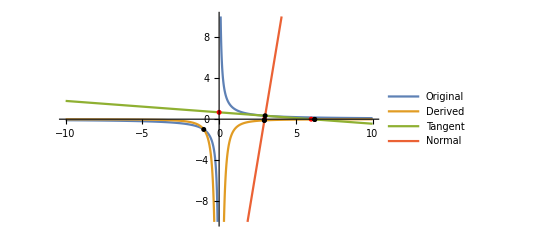
Derivative | Tangent: x = 3 | Normal: x = 3 | Integrated (No abitrary constant) | Graph
-1/x^2 | 2/3-x/9 | 9 x-80/3 | log(x) | -Graphics-

```mathematica
Dio[1/x,3,{x},10]
```

### Probability Normal Distribution

```mathematica
PrNoramlDistPlot[mean_,sd_,{x_,Optional[x1_,Null],Optional[x2_,Null]},Optional[value_,Null]]:=Module[{Line,Area},
Line=Plot[1/(sd Sqrt[2Pi])E^(-1/2((x-mean)/sd)^2),{x,mean-sd*4,mean+sd*4},AxesLabel->{": (standard deviation)" sd,"Probability X=x"}];

If[x1=!=Null And x2 =!=Null ,{Area=Plot[1/(sd Sqrt[2Pi])E^(-1/2((x-mean)/sd)^2),{x,If[x1==-Infinity,mean-sd*4,x1],If[x2==Infinity,mean+sd*4,x2]},Filling->Axis,PlotRange->PlotRange[Line]],{Print[Show[Line,Area]],Return[Print["Pr(", x1<X<x2, ")= ",NProbability[x1<X<x2,X\[Distributed]NormalDistribution[mean,sd]]]]}},Print[Show[Line]]];
If[value=!=Null,Print["Pr(",value,")=",
NProbability[value,x\[Distributed]NormalDistribution[mean,sd]]]];
]
```

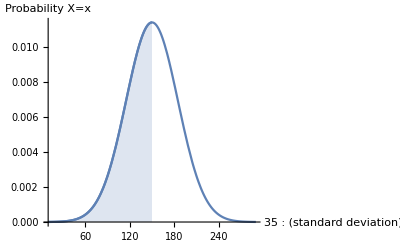

Pr(-∞<X<150)= 0.5

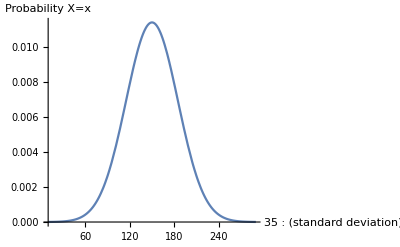

Pr(x>150\[Conditioned]x>100)=0.541456

```mathematica
PrNoramlDistPlot[150,35,{x,-Infinity,150}]
PrNoramlDistPlot[150,35,{x},x>150\[Conditioned]x>100]
```

### Binomial Distribution

```mathematica
BDPr[trials_,probability_, {Optional[value_, Null],X_},Optional[times_,-1]]:=
Module[{list},
list=Table[{ n,Probability[X==n,X \[Distributed]BinomialDistribution[trials,probability]]},{n,If[times==-1,trials,times]}];
If[value =!= Null,AppendTo[list,{value,Probability[value,X\[Distributed]BinomialDistribution[trials,probability]]}]];
AppendTo[list,{"E[x]",Mean[BinomialDistribution[trials,probability]]}];
AppendTo[list,{"Var[x]",Variance[BinomialDistribution[trials,probability]]}];
AppendTo[list,{"Sd[x]",StandardDeviation[BinomialDistribution[trials,probability]]}];
list//TableForm]
```

```mathematica
BDPr[6,0.6,{X==3,X},1]
```

1 | 0.036864
X==3 | 0.27648
E[x] | 3.6
Var[x] | 1.44
Sd[x] | 1.2